# Diaphorina citri en red: un recorrido rápido

Demo para discusión con el asesor. Orden: Red -> Función -> Evolución -> Resultados -> Comparación.

## 0. Funciones necesarias

Solo lo que usamos aquí: el modelo de un nodo (para comparar), el generador de topologías, y el solver de red.

```mathematica
ClearAll[SolveSystem];
SolveSystem[δ_,T_,{{r1_,b12_,b13_,a1_,c1_},{r2_,b21_,b24_,a2_,c2_},{r3_,b31_,a3_,c3_},{r4_,b42_,a4_,c4_}},{Di0_,B0_,x30_,x40_,tt_}]:=
NDSolve[{
 x1'[t]==x1[t]*(r1+b12*x2[t]+b13*x3[t]-(a1+c1*(b12*x2[t]+b13*x3[t]))*x1[t]),
 x2'[t]==x2[t]*(r2+b21*x1[t]+b24*x4[t]-(a2+c2*(b21*x1[t]+b24*x4[t]))*x2[t]),
 x3'[t]==x3[t]*(r3+b31*x1[t]-(a3+c3*b31*x1[t])*x3[t]),
 x4'[t]==x4[t]*(r4+b42*x2[t]-(a4+c4*b42*x2[t])*x4[t]),
 x1[0]==Di0, x2[0]==B0, x3[0]==x30, x4[0]==x40,
 WhenEvent[Mod[t,T]==0 && t>0, x3[t]->x3[t]+δ]
},{x1,x2,x3,x4},{t,0,tt},Method->{"TimeIntegration"->"ExplicitRungeKutta"}]

ClearAll[MakeTopology];
MakeTopology[name_String, n_Integer, seed_: 1] := (
    SeedRandom[seed];
    Switch[name,
        "Path", PathGraph[Range[n]],
        "Cycle", CycleGraph[n],
        "Star", StarGraph[n],
        "Complete", CompleteGraph[n],
        "Random", RandomGraph[BernoulliGraphDistribution[n, 0.4]],
        "SmallWorld", RandomGraph[WattsStrogatzGraphDistribution[n, 0.2, Max[1, Min[2, Floor[n/2] - 1]]]],
        "ScaleFree", RandomGraph[BarabasiAlbertGraphDistribution[n, Min[2, n - 1]]],
        _, Missing["UnknownTopology", name]
    ]
);

ClearAll[SolveNetworkData];
SolveNetworkData[graph_?GraphQ, Dd_, Dt_, δ_, T_,
    {{r1_, b12_, b13_, a1_, c1_},
     {r2_, b21_, b24_, a2_, c2_},
     {r3_, b31_, a3_, c3_},
     {r4_, b42_, a4_, c4_}},
    {Di0_, B0_, x30_, x40_, tt_},
    releaseNodes_: All
] := Module[{L, n, eqs, ics, vars, sol, events, targets},
    L = Normal @ KirchhoffMatrix[graph];
    n = VertexCount[graph];

    eqs = Flatten @ {
        Table[
            x1[i]'[t] == x1[i][t]*(r1 + b12*x2[i][t] + b13*x3[i][t] -
                (a1 + c1*(b12*x2[i][t] + b13*x3[i][t]))*x1[i][t]) -
                Dd*Sum[L[[i, j]] x1[j][t], {j, n}],
            {i, n}
        ],
        Table[
            x2[i]'[t] == x2[i][t]*(r2 + b21*x1[i][t] + b24*x4[i][t] -
                (a2 + c2*(b21*x1[i][t] + b24*x4[i][t]))*x2[i][t]),
            {i, n}
        ],
        Table[
            x3[i]'[t] == x3[i][t]*(r3 + b31*x1[i][t] -
                (a3 + c3*b31*x1[i][t])*x3[i][t]) -
                Dt*Sum[L[[i, j]] x3[j][t], {j, n}],
            {i, n}
        ],
        Table[
            x4[i]'[t] == x4[i][t]*(r4 + b42*x2[i][t] -
                (a4 + c4*b42*x2[i][t])*x4[i][t]),
            {i, n}
        ]
    };

    ics = Flatten @ {
        Table[x1[i][0] == Di0[[i]], {i, n}],
        Table[x2[i][0] == B0[[i]], {i, n}],
        Table[x3[i][0] == x30[[i]], {i, n}],
        Table[x4[i][0] == x40[[i]], {i, n}]
    };

    vars = Flatten @ {
        Table[x1[i], {i, n}],
        Table[x2[i], {i, n}],
        Table[x3[i], {i, n}],
        Table[x4[i], {i, n}]
    };

    targets = If[releaseNodes === All, Range[n], releaseNodes];
    events = If[δ == 0 || targets === {}, {},
        {WhenEvent[Mod[t, T] == 0 && t > 0,
            Evaluate @ Table[x3[i][t] -> x3[i][t] + δ, {i, targets}]]}
    ];

    sol = First @ NDSolve[
        Join[eqs, ics, events],
        vars, {t, 0, tt},
        Method -> {"TimeIntegration" -> "ExplicitRungeKutta"}
    ];

    <|
        "Solution" -> sol, "Graph" -> graph, "N" -> n,
        "Dd" -> Dd, "Dt" -> Dt, "Delta" -> δ, "T" -> T, "tt" -> tt,
        "ReleaseNodes" -> targets
    |>
];

ClearAll[NodeIF];
NodeIF[data_Association, var_, i_] := var[i] /. data["Solution"];
```

## 1. Red -- la topología

Cada nodo es una localidad (huerto). Empezamos con 5 nodos en una red tipo "camino": cada huerto solo intercambia con su vecino inmediato.

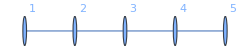

```mathematica
n = 5;
graph = MakeTopology["Path", n];
Graph[graph, VertexLabels -> "Name", ImageSize -> 250]
```

## 2. Función -- el modelo en cada nodo

Mismos parámetros y ecuaciones del paper de un solo nodo, replicados en cada localidad. Diaphorina citri (x1) y Tamarixia radiata (x3) pueden moverse entre nodos vecinos (tasas Dd, Dt); brotes (x2) y vigor de planta (x4) se quedan en su nodo.

```mathematica
as = 0.000555; cs = 0.005;
param1 = {-0.2, 0.04, -0.01, as, cs};
param2 = {-0.72, -0.01, 0.054, as, cs};
param3 = {-0.3, 0.01, as, cs};
param4 = {0.72, -0.072, as, cs};
params = {param1, param2, param3, param4};
```

## 3. Evolución -- resolver el sistema

Un brote puntual: el nodo 1 arranca con 200 Diaphorina (foco), el resto en 20. Liberación periódica de Tamarixia (δ=35 cada T=15) en todos los nodos. Difusión Dd=Dt=0.03.

```mathematica
tt = 100;
ics = {Prepend[ConstantArray[20, n - 1], 200], ConstantArray[10, n], ConstantArray[15, n], ConstantArray[30, n], tt};
netData = SolveNetworkData[graph, 0.03, 0.03, 35, 15, params, ics];
```

## 4. Resultados -- qué pasó en cada nodo?

Diaphorina citri (x1) en cada nodo a lo largo del tiempo. El nodo 1 (el foco del brote) parte muy por encima del resto.

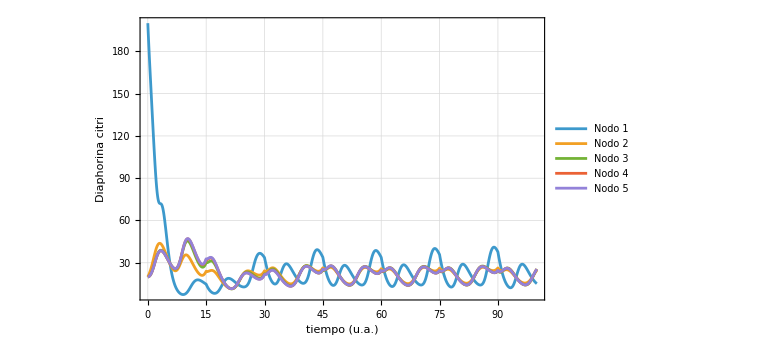

```mathematica
Plot[Evaluate[Table[NodeIF[netData, x1, i][t], {i, n}]], {t, 0, tt},
  PlotLegends -> Table["Nodo " <> ToString[i], {i, n}],
  FrameLabel -> {"tiempo (u.a.)", "Diaphorina citri"}, Frame -> True,
  GridLines -> Automatic, GridLinesStyle -> Directive[Dashed], ImageSize -> Large,PlotRange->All]
```

## 5. Comparación -- \[QuestionMark]importó la red?

(a) El nodo 1 en la red, contra el mismo huerto aislado (modelo de un solo nodo, misma condición inicial). La diferencia es exactamente el efecto de estar conectado.

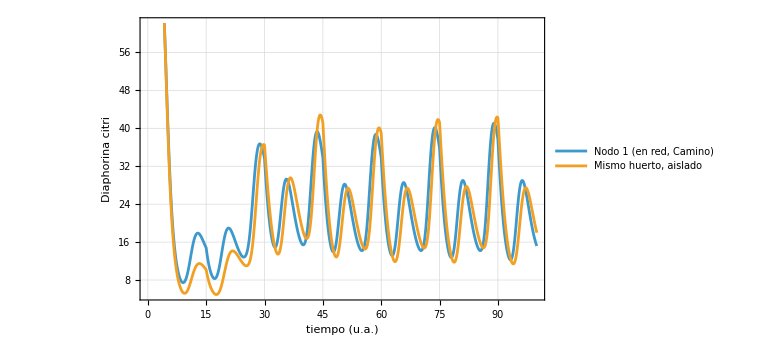

```mathematica
singleSol = SolveSystem[35, 15, params, {200, 10, 15, 30, tt}];
Plot[Evaluate[{NodeIF[netData, x1, 1][t], (x1 /. First[singleSol])[t]}], {t, 0, tt},
  PlotLegends -> {"Nodo 1 (en red, Camino)", "Mismo huerto, aislado"},
  FrameLabel -> {"tiempo (u.a.)", "Diaphorina citri"}, Frame -> True,
  GridLines -> Automatic, GridLinesStyle -> Directive[Dashed], ImageSize -> Large]
```

(b) La misma pregunta, pero cambiando solo la topología: Camino (poco conectada) contra Completa (todos los nodos conectados entre sí).

```mathematica
graphComplete = MakeTopology["Complete", n]
```

-Graphics-

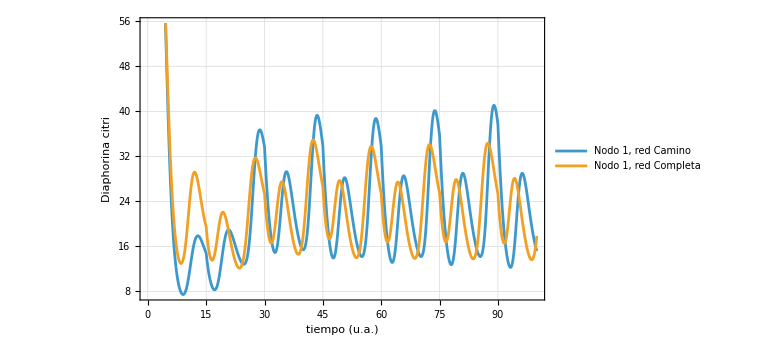

```mathematica
netDataComplete = SolveNetworkData[graphComplete, 0.03, 0.03, 35, 15, params, ics];
Plot[Evaluate[{NodeIF[netData, x1, 1][t], NodeIF[netDataComplete, x1, 1][t]}], {t, 0, tt},
  PlotLegends -> {"Nodo 1, red Camino", "Nodo 1, red Completa"},
  FrameLabel -> {"tiempo (u.a.)", "Diaphorina citri"}, Frame -> True,
  GridLines -> Automatic, GridLinesStyle -> Directive[Dashed], ImageSize -> Large]
```